## Definiciones

### Operadores

#### Coin

```mathematica
n[α_,ϕ_]:={Sin[α]Cos[ϕ],Sin[α]Sin[ϕ],Cos[α]}
```

```mathematica
Paulis=PauliMatrix/@Range[3];
```

```mathematica
expCoin[θ_,α_,ϕ_]:=MatrixExp[(-ⅈ θ)/2(n[α,ϕ].Paulis)]
```

```mathematica
Coin[θ_,α_,ϕ_,t_Integer]:=KroneckerProduct[SparseArray[Table[{i,i}->1.,{i,2 t+1}]],SparseArray[expCoin[θ,α,ϕ]]]
```

#### Shift

```mathematica
Shift[t_Integer]:=SparseArray[Join[Table[{i,i+2},{i,Range[2,#-2,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1.,{#,#}]&[2*(2*t+1)]
```

#### Unitaria

```mathematica
Unitary[θ_,α_,ϕ_,t_Integer]:=Shift[t].Coin[θ,α,ϕ,t]
```

```mathematica
Unitary[π/10,π/10,π/5,1]
```

SparseArray[…]

### Funciones cálculos

#### Estado final de la caminata después de t pasos

```mathematica
DQWL[ψ0_,θ_,α_,ϕ_,t_Integer]:=
Module[{psi},
psi=ψ0;
Do[psi=Chop[#.ArrayPad[psi,2]]&[Unitary[θ,α,ϕ,i]],{i,t}];
psi
]
```

#### Distribución de probabilidad

```mathematica
PosProbDistrib[psi_,tmax_]:=Chop[Total[Abs[psi[[#;;#+1]]]^2]&/@Range[1,2(2tmax+1),2]]
```

#### Distribución de probabilidad para cada uno de los pasos

```mathematica
ClearAll[ProbDisTime]
```

```mathematica
ProbDisTime[ψ0_,θ_,α_,ϕ_,t_Integer]:=
Module[{psi,probs,p},
psi=ψ0;
p=Table[
probs=PosProbDistrib[psi,i-1];
psi=Chop[#.ArrayPad[psi,2]]&[Unitary[N@θ,N@α,N@ϕ,i]];
ArrayPad[probs,t-(i-1)],{i,t+1}
];
p
]
```

#### Valor de expectación

```mathematica
ExpecValue[posProbDisTime_List, t_Integer]:=Flatten[posProbDisTime.{{Range[-t,t]}ᵀ}ᵀ]
```

### Funciones gráficas

#### Colores

```mathematica
Midnight=RGBColor["#311441"];
Sky=RGBColor["#35A3FA"];
AcuaGreen=RGBColor["#47F884"];
DirtyYellow=RGBColor["#E1DC46"];
HotOrange=RGBColor["#F4651D"];
Wine=RGBColor["#7D0402"];
ArticleColors=(Blend[{Midnight,Sky,AcuaGreen,DirtyYellow,HotOrange,Wine},#]&);
```

#### Probabilidad respecto al tiempo

```mathematica
PlotPosProbDisTime[posProbDis_List]:=
ArrayPlot[posProbDis,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
DataReversed->True,
PlotLegends->Automatic,
ColorFunction->ArticleColors,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicks->{{Table[{i,i-1,0},{i,1,(2t+1-1)/2+1,(2t+1-1)/12}],None},{Table[{i,i-1-t,0},{i,1,2t+1,t}],None}},
FrameTicksStyle->13,
PlotRangePadding->0
]
```

#### Valor de expectación respecto al tiempo

```mathematica
PlotExpecValue[expecValue_List,θ_,α_,ϕ_,t_,opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,t],expecValue}ᵀ,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
Mesh->All,
PlotStyle->Thickness[0.005],
GridLines->{Range[Automatic,Automatic,50],Range[Automatic,Automatic,20]},
GridLinesStyle->Thin,
Evaluate@opts
]
```

```mathematica
PlotExpecValue[{expecValues__List},θ_,α_,ϕ_,t_,opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,t],#}ᵀ&/@{expecValues},
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
PlotStyle->Thickness[0.005],
Mesh->All,
Evaluate@opts
]
```

#### Determinar si la estrategia es ganadora o perdedora

```mathematica
WinningQ[lista_List] := 
  Which[
    OrderedQ[lista], "Ganadora",
    OrderedQ[lista, GreaterEqual], "Perdedora",
    True, "No se puede determinar"
  ]
```

#### Revisar si la estrategia es ganadora o perdedora fijando θ y α, variando ϕ

```mathematica
VaryingPhi[psi0_,θ_,α_,nϕ_Integer,t_Integer]:=Table[
Module[{ϕ,probDistTime,expval},
ϕ=i *2π/nϕ;
probDistTime=ProbDisTime[psi0,θ,α,ϕ,t];
expval=ExpecValue[probDistTime,t];
{WinningQ[expval],
PlotExpecValue[expval,θ,α,ϕ,t,
PlotLabel->Column[
{Row[{"θ = ",θ,",  α = ",α,",  ϕ = ",ϕ}],
Row[{ToString[WinningQ[expval]]}]
},
Alignment->Center
],
ImageSize->300
]
}
],
{i,1,nϕ}
]
```

#### Revisar si la estrategia es ganadora o perdedora fijando θ , variando α y ϕ

```mathematica
VaryingAlpha[psi0_,θ_,nα_Integer,nϕ_Integer,t_Integer]:=Table[
Module[{α},
α=j*π/nα;
VaryingPhi[psi0,θ,α,nϕ,t]
],
{j,1,nα}
]
```

#### Revisar si la estrategia es ganadora o perdedora variando θ, α y ϕ

```mathematica
VaryingTheta[psi0_,nθ_Integer,nα_Integer,nϕ_Integer,t_Integer]:=Table[
Module[{θ},
θ=k*4π/nθ;
VaryingAlpha[psi0,θ,nα,nϕ,t]
],
{k,1,nθ}
]
```

## Estado inicial 0para la moneda

θ ∈ [0, 4π); α ∈ (0, π]; ϕ ∈ (0, 2π].

## θ = π/10, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=π/10;
nα=10;
nϕ=10;
t=100;
res1=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = π/10, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res1[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/10, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res1[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/10, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
res1[[3,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/10, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
res1[[4,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/10, α = π/2, ϕ ∈ (0, 2π]

```mathematica
res1[[5,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/10, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
res1[[6,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/10, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
res1[[7,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/10, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
res1[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/10, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res1[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/10, α = π, ϕ ∈ (0, 2π]

```mathematica
res1[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=π/5;
nα=10;
nϕ=10;
t=100;
res2=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res2[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res2[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
res2[[3,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
res2[[4,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
res2[[5,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
res2[[6,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
res2[[7,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
res2[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res2[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
res2[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 3π/10, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=3π/10;
nα=10;
nϕ=10;
t=100;
res3=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 3π/10, α = π/10, ϕ ∈ (0, 2π]

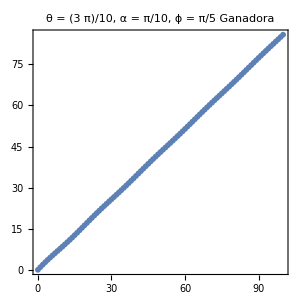
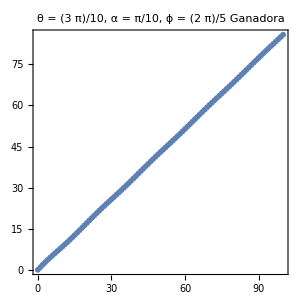
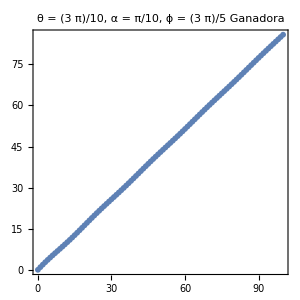
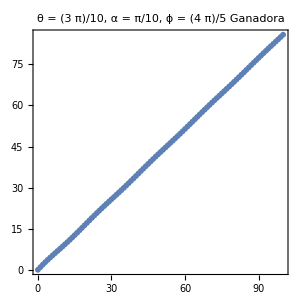
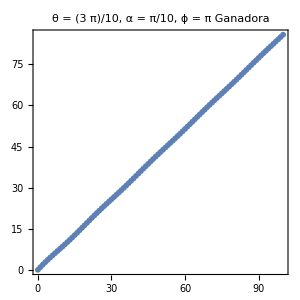
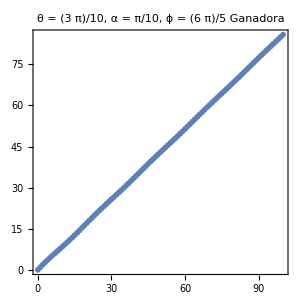
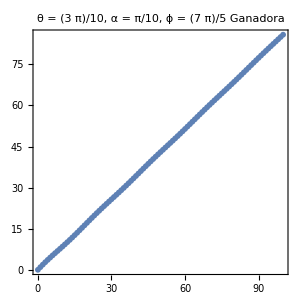
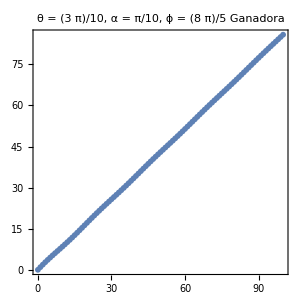

```mathematica
res3[[1,All,2]]
```

### θ = 3π/10, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res3[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 3π/10, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
res3[[3,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 3π/10, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
res3[[4,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 3π/10, α = π/2, ϕ ∈ (0, 2π]

```mathematica
res3[[5,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 3π/10, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
res3[[6,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 3π/10, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
res3[[7,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 3π/10, α = 4π/5, ϕ ∈ (0, 2π]

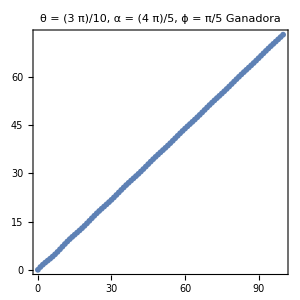
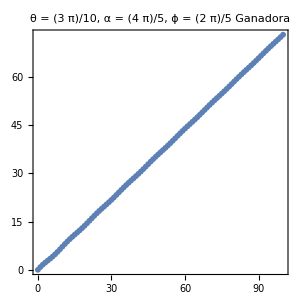
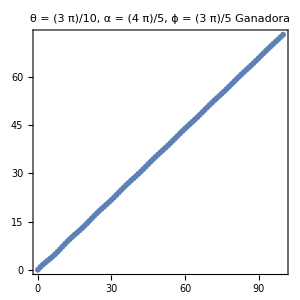
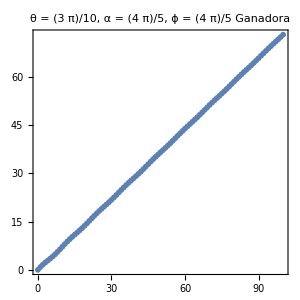
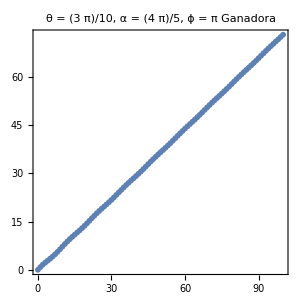
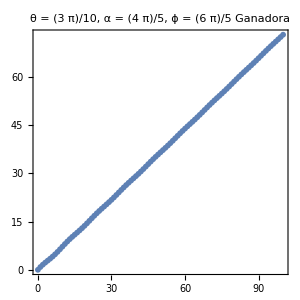
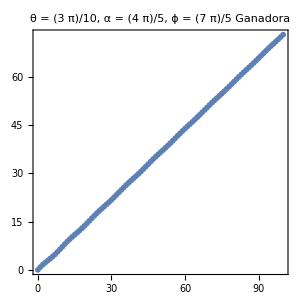
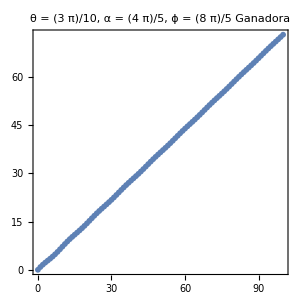

```mathematica
res3[[8,All,2]]
```

### θ = 3π/10, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res3[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 3π/10, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res3[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 2π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=2π/5;
nα=10;
nϕ=10;
t=100;
res4=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 2π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res4[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res4[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
res4[[3,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
res4[[4,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
res4[[5,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
res4[[6,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
res4[[7,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
res4[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res4[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
res4[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = π/2, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=π/2;
nα=10;
nϕ=10;
t=100;
res5=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = π/2, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res5[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/2, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res5[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/2, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
res5[[3,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/2, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
res5[[4,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/2, α = π/2, ϕ ∈ (0, 2π]

```mathematica
res5[[5,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/2, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
res5[[6,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/2, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
res5[[7,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/2, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
res5[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/2, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res5[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/2, α = π, ϕ ∈ (0, 2π]

```mathematica
res5[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 3π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=3π/5;
nα=10;
nϕ=10;
t=100;
res6=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 3π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res6[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 3π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res6[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 3π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
res6[[3,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 3π/5, α = 2π/5, ϕ ∈ (0, 2π]

Prácticamente ganadoras

```mathematica
res6[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 3π/5, α = π/2, ϕ ∈ (0, 2π]

Prácticamente ganadoras

```mathematica
res6[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 3π/5, α = 3π/5, ϕ ∈ (0, 2π]

Prácticamente ganadoras

```mathematica
res6[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 3π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
res6[[7,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 3π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
res6[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 3π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res6[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 3π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
res6[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 7π/10, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=7π/10;
nα=10;
nϕ=10;
t=100;
res7=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 7π/10, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res7[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 7π/10, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res7[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 7π/10, α = 3π/10, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res7[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/10, α = 2π/5, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res7[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/10, α = π/2, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res7[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/10, α = 3π/5, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res7[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/10, α = 7π/10, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res7[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/10, α = 4π/5, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res7[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 7π/10, α = 9π/10, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res7[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 7π/10, α = π, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res7[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 4π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=4π/5;
nα=10;
nϕ=10;
t=100;
res8=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 4π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res8[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 4π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res8[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 4π/5, α = 3π/10, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res8[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = 2π/5, ϕ ∈ (0, 2π]

Prácticamente ganadora (primeros datos por debajo de 0)

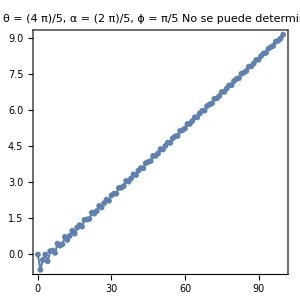
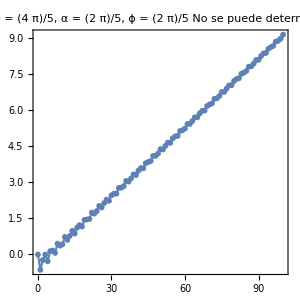
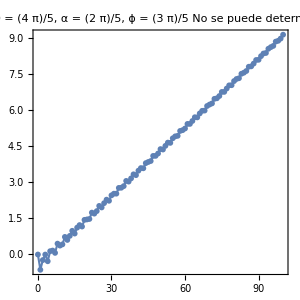
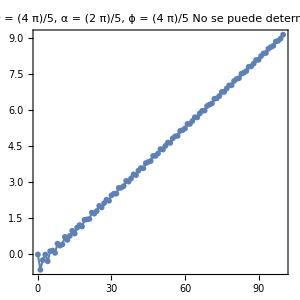
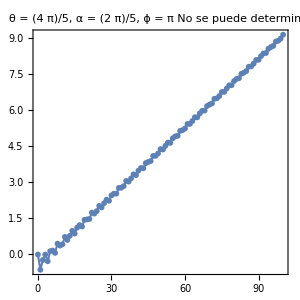
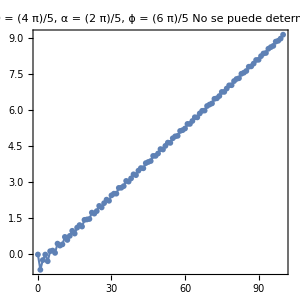
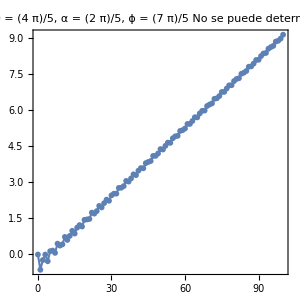
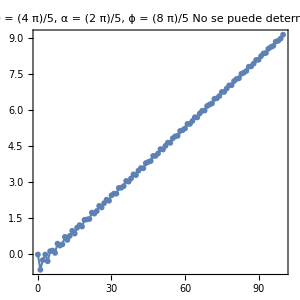

```mathematica
res8[[4,All,2]]
```

### θ = 4π/5, α = π/2, ϕ ∈ (0, 2π]

Prácticamente ganadora (primeros datos por debajo de 0)

```mathematica
res8[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = 3π/5, ϕ ∈ (0, 2π]

Prácticamente ganadora (primeros datos por debajo de 0)

```mathematica
res8[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = 7π/10, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res8[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
res8[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 4π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res8[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 4π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
res8[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 9π/10, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=9π/10;
nα=10;
nϕ=10;
t=100;
res9=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 9π/10, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res9[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 9π/10, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res9[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 9π/10, α = 3π/10, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res9[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 9π/10, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
res9[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 9π/10, α = π/2, ϕ ∈ (0, 2π]

```mathematica
res9[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 9π/10, α = 3π/5, ϕ ∈ (0, 2π]

Prácticamente ganadora (primeros datos por debajo de 0)

```mathematica
res9[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 9π/10, α = 7π/10, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res9[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 9π/10, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
res9[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 9π/10, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res9[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 9π/10, α = π, ϕ ∈ (0, 2π]

```mathematica
res9[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = π, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=π;
nα=10;
nϕ=10;
t=100;
res10=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = π, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res10[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res10[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π, α = 3π/10, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res10[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = 2π/5, ϕ ∈ (0, 2π]

Prácticamente ganadora (primeros datos por debajo de 0)

```mathematica
res10[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = π/2, ϕ ∈ (0, 2π]

Simétrica

```mathematica
res10[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = 3π/5, ϕ ∈ (0, 2π]

Prácticamente ganadora (primeros datos por debajo de 0)

```mathematica
res10[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = 7π/10, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res10[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
res10[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res10[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π, α = π, ϕ ∈ (0, 2π]

```mathematica
res10[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 6π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=6π/5;
nα=10;
nϕ=10;
t=100;
res11=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 6π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res11[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 6π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res11[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 6π/5, α = 3π/10, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res11[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = 2π/5, ϕ ∈ (0, 2π]

Prácticamente ganadora (primeros datos por debajo de 0)

```mathematica
res11[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = π/2, ϕ ∈ (0, 2π]

Prácticamente ganadora (primeros datos por debajo de 0)

```mathematica
res11[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = 3π/5, ϕ ∈ (0, 2π]

Prácticamente ganadora (primeros datos por debajo de 0)

```mathematica
res11[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = 7π/10, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res11[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
res11[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 6π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res11[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 6π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
res11[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 7π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=7π/5;
nα=10;
nϕ=10;
t=100;
res12=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 7π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res12[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 7π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res12[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 7π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
res12[[3,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 7π/5, α = 2π/5, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res12[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/5, α = π/2, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res12[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/5, α = 3π/5, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res12[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
res12[[7,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 7π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
res12[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 7π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res12[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 7π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
res12[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 8π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=8π/5;
nα=10;
nϕ=10;
t=100;
res13=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 8π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res13[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 8π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res13[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 8π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
res13[[3,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 8π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
res13[[4,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 8π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
res13[[5,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 8π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
res13[[6,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 8π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
res13[[7,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 8π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
res13[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 8π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res13[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 8π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
res13[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 9π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=9π/5;
nα=10;
nϕ=10;
t=100;
res14=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 9π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res14[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 9π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res14[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 9π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
res14[[3,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 9π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
res14[[4,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 9π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
res14[[5,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 9π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
res14[[6,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 9π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
res14[[7,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 9π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
res14[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 9π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res14[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 9π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
res14[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 2π, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=2π;
nα=10;
nϕ=10;
t=100;
res15=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 2π, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res15[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res15[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
res15[[3,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
res15[[4,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π, α = π/2, ϕ ∈ (0, 2π]

```mathematica
res15[[5,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
res15[[6,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
res15[[7,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
res15[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res15[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π, α = π, ϕ ∈ (0, 2π]

```mathematica
res15[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 12π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=12π/5;
nα=10;
nϕ=10;
t=100;
res16=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 12π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res16[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 12π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res16[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 12π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
res16[[3,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 12π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
res16[[4,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 12π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
res16[[5,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 12π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
res16[[6,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 12π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
res16[[7,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 12π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
res16[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 12π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res16[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 12π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
res16[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 14π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=14π/5;
nα=10;
nϕ=10;
t=100;
res17=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 14π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res17[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 14π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res17[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 14π/5, α = 3π/10, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res17[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 14π/5, α = 2π/5, ϕ ∈ (0, 2π]

Prácticamente ganadora (primeros datos por debajo de 0)

```mathematica
res17[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 14π/5, α = π/2, ϕ ∈ (0, 2π]

Prácticamente ganadora (primeros datos por debajo de 0)

```mathematica
res17[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 14π/5, α = 3π/5, ϕ ∈ (0, 2π]

Prácticamente ganadora (primeros datos por debajo de 0)

```mathematica
res17[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 14π/5, α = 7π/10, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res17[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 14π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
res17[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 14π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res17[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 14π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
res17[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 16π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=16π/5;
nα=10;
nϕ=10;
t=100;
res18=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 16π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res18[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 16π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res18[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 16π/5, α = 3π/10, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res18[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 16π/5, α = 2π/5, ϕ ∈ (0, 2π]

Prácticamente ganadora (primeros datos por debajo de 0)

```mathematica
res18[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 16π/5, α = π/2, ϕ ∈ (0, 2π]

Prácticamente ganadora (primeros datos por debajo de 0)

```mathematica
res18[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 16π/5, α = 3π/5, ϕ ∈ (0, 2π]

Prácticamente ganadora (primeros datos por debajo de 0)

```mathematica
res18[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 16π/5, α = 7π/10, ϕ ∈ (0, 2π]

Prácticamente ganadora

```mathematica
res18[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 16π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
res18[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 16π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res18[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 16π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
res18[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 18π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=18π/5;
nα=10;
nϕ=10;
t=100;
res19=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 18π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res19[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 18π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res19[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 18π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
res19[[3,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 18π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
res19[[4,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 18π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
res19[[5,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 18π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
res19[[6,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 18π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
res19[[7,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 18π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
res19[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 18π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res19[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 18π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
res19[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 4π, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={1.,0.};
θ=4π;
nα=10;
nϕ=10;
t=100;
res20=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 4π, α = π/10, ϕ ∈ (0, 2π]

```mathematica
res20[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 4π, α = π/5, ϕ ∈ (0, 2π]

```mathematica
res20[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 4π, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
res20[[3,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 4π, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
res20[[4,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 4π, α = π/2, ϕ ∈ (0, 2π]

```mathematica
res20[[5,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 4π, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
res20[[6,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 4π, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
res20[[7,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 4π, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
res20[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 4π, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
res20[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 4π, α = π, ϕ ∈ (0, 2π]

```mathematica
res20[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## Estado inicial 1para la moneda

θ ∈ [0, 4π); α ∈ (0, π]; ϕ ∈ (0, 2π].

## θ = π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={0.,1.};
θ=π/5;
nα=10;
nϕ=10;
t=100;
r11=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
r11[[1,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
r11[[2,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
r11[[3,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
r11[[4,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
r11[[5,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
r11[[6,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
r11[[7,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
r11[[8,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
r11[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
r11[[10,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

## θ = 2π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={0.,1.};
θ=2π/5;
nα=10;
nϕ=10;
t=100;
r12=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 2π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
r12[[1,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 2π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
r12[[2,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 2π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
r12[[3,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 2π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
r12[[4,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 2π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
r12[[5,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 2π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
r12[[6,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 2π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
r12[[7,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 2π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
r12[[8,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 2π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
r12[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 2π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
r12[[10,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

## θ = 3π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={0.,1.};
θ=3π/5;
nα=10;
nϕ=10;
t=100;
r13=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 3π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
r13[[1,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 3π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
r13[[2,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 3π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
r13[[3,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 3π/5, α = 2π/5, ϕ ∈ (0, 2π]

Prácticamente perdedoras

```mathematica
r13[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 3π/5, α = π/2, ϕ ∈ (0, 2π]

Prácticamente perdedoras

```mathematica
r13[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 3π/5, α = 3π/5, ϕ ∈ (0, 2π]

Prácticamente perdedoras

```mathematica
r13[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 3π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
r13[[7,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 3π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
r13[[8,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 3π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
r13[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 3π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
r13[[10,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

## θ = 4π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={0.,1.};
θ=4π/5;
nα=10;
nϕ=10;
t=100;
r14=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 4π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
r14[[1,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 4π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
r14[[2,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 4π/5, α = 3π/10, ϕ ∈ (0, 2π]

Prácticamente perdedoras

```mathematica
r14[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = 2π/5, ϕ ∈ (0, 2π]

Prácticamente perdedoras (primeros datos por arriba de 0)

```mathematica
r14[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = π/2, ϕ ∈ (0, 2π]

Prácticamente perdedoras (primeros datos por arriba de 0)

```mathematica
r14[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = 3π/5, ϕ ∈ (0, 2π]

Prácticamente perdedoras (primeros datos por arriba de 0)

```mathematica
r14[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = 7π/10, ϕ ∈ (0, 2π]

Prácticamente perdedoras

```mathematica
r14[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
r14[[8,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 4π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
r14[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 4π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
r14[[10,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

## θ = π, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={0.,1.};
θ=π;
nα=10;
nϕ=10;
t=100;
r15=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = π, α = π/10, ϕ ∈ (0, 2π]

```mathematica
r15[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π, α = π/5, ϕ ∈ (0, 2π]

```mathematica
r15[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π, α = 3π/10, ϕ ∈ (0, 2π]

Prácticamente perdedoras

```mathematica
r15[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = 2π/5, ϕ ∈ (0, 2π]

Prácticamente perdedoras (primeros arriba por debajo de 0)

```mathematica
r15[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = π/2, ϕ ∈ (0, 2π]

Simétrica

```mathematica
r15[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = 3π/5, ϕ ∈ (0, 2π]

Prácticamente perdedoras (primeros arriba por debajo de 0)

```mathematica
r15[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = 7π/10, ϕ ∈ (0, 2π]

Prácticamente perdedoras

```mathematica
r15[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
r15[[8,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = π, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
r15[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = π, α = π, ϕ ∈ (0, 2π]

```mathematica
r15[[10,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

## θ = 6π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={0.,1.};
θ=6π/5;
nα=10;
nϕ=10;
t=100;
r16=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 6π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
r16[[1,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 6π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
r16[[2,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 6π/5, α = 3π/10, ϕ ∈ (0, 2π]

Prácticamente perdedoras

```mathematica
r16[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = 2π/5, ϕ ∈ (0, 2π]

Prácticamente perdedoras (primeros datos por arriba de 0)

```mathematica
r16[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = π/2, ϕ ∈ (0, 2π]

Prácticamente perdedoras (primeros datos por arriba de 0)

```mathematica
r16[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = 3π/5, ϕ ∈ (0, 2π]

Prácticamente perdedoras (primeros datos por arriba de 0)

```mathematica
r16[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = 7π/10, ϕ ∈ (0, 2π]

Prácticamente perdedoras

```mathematica
r16[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
r16[[8,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 6π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
r16[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 6π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
r16[[10,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

## θ = 7π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={0.,1.};
θ=7π/5;
nα=10;
nϕ=10;
t=100;
r17=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 7π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
r17[[1,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 7π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
r17[[2,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 7π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
r17[[3,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 7π/5, α = 2π/5, ϕ ∈ (0, 2π]

Prácticamente perdedoras

```mathematica
r17[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/5, α = π/2, ϕ ∈ (0, 2π]

Prácticamente perdedoras

```mathematica
r17[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/5, α = 3π/5, ϕ ∈ (0, 2π]

Prácticamente perdedoras

```mathematica
r17[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
r17[[7,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 7π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
r17[[8,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 7π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
r17[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 7π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
r17[[10,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

## θ = 8π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={0.,1.};
θ=8π/5;
nα=10;
nϕ=10;
t=100;
r18=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 8π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
r18[[1,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 8π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
r18[[2,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 8π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
r18[[3,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 8π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
r18[[4,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 8π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
r18[[5,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 8π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
r18[[6,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 8π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
r18[[7,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 8π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
r18[[8,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 8π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
r18[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 8π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
r18[[10,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

## θ = 9π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={0.,1.};
θ=9π/5;
nα=10;
nϕ=10;
t=100;
r19=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 9π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
r19[[1,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
r19[[2,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
r19[[3,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
r19[[4,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
r19[[5,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
r19[[6,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
r19[[7,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
r19[[8,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
r19[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
r19[[10,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

## θ = 2π, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0={0.,1.};
θ=2π;
nα=10;
nϕ=10;
t=100;
r110=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 2π, α = π/10, ϕ ∈ (0, 2π]

```mathematica
r110[[1,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 2π, α = π/5, ϕ ∈ (0, 2π]

```mathematica
r110[[2,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 2π, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
r110[[3,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 2π, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
r110[[4,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 2π, α = π/2, ϕ ∈ (0, 2π]

```mathematica
r110[[5,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 2π, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
r110[[6,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 2π, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
r110[[7,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 2π, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
r110[[8,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 2π, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
r110[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 2π, α = π, ϕ ∈ (0, 2π]

```mathematica
r110[[10,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

## Estado inicial +_xpara la moneda

θ ∈ [0, 4π); α ∈ (0, π]; ϕ ∈ (0, 2π].

## θ = π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2]{1.,1.};
θ=π/5;
nα=10;
nϕ=10;
t=100;
rplusx1=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx1[[1,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx1[[2,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx1[[3,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = 2π/5, ϕ ∈ (0, 2π]

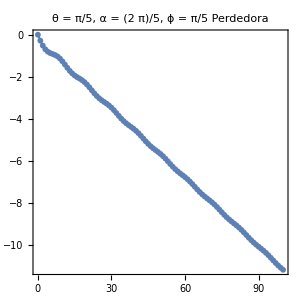
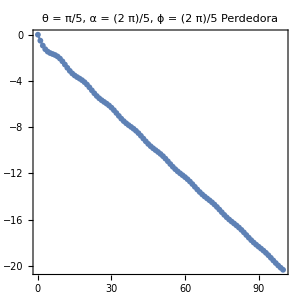
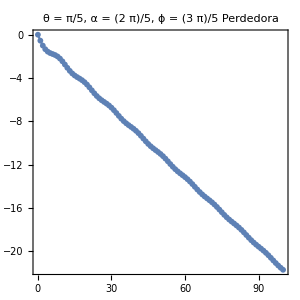
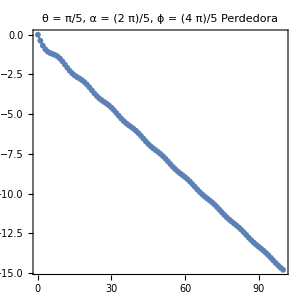
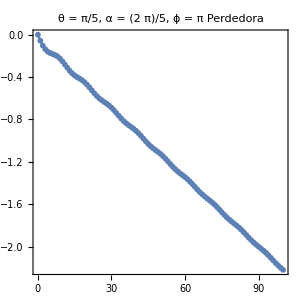
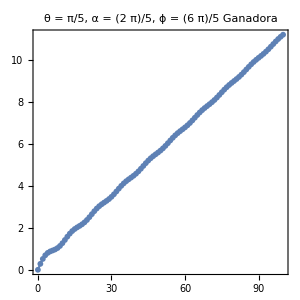
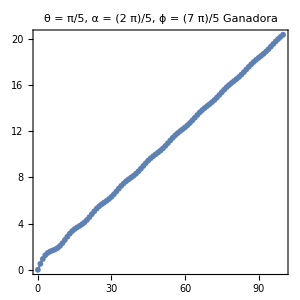
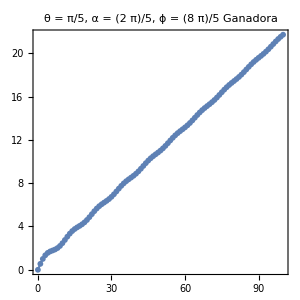

```mathematica
rplusx1[[4,All,2]]
```

### θ = π/5, α = π/2, ϕ ∈ (0, 2π]

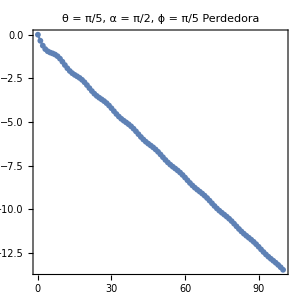
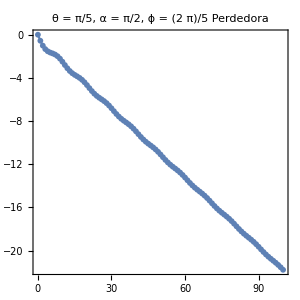
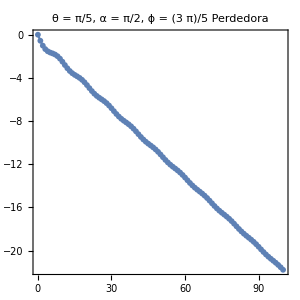
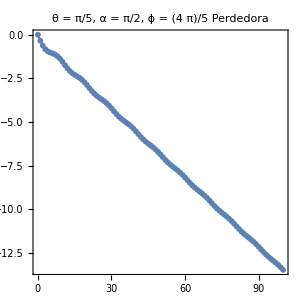
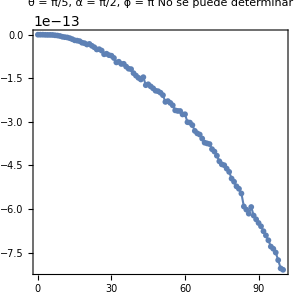
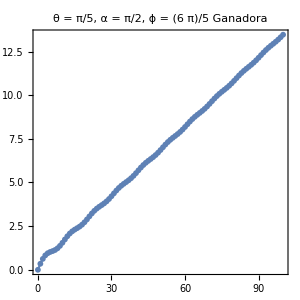
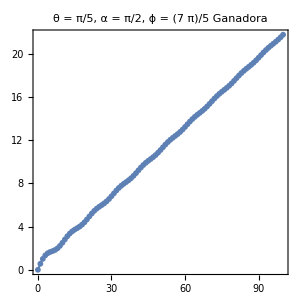
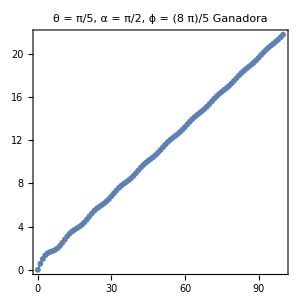

```mathematica
rplusx1[[5,All,2]]
```

### θ = π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx1[[6,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora}

### θ = π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx1[[7,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora}

### θ = π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx1[[8,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora}

### θ = π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx1[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora}

### θ = π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusx1[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 2π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2]{1.,1.};
θ=2π/5;
nα=10;
nϕ=10;
t=100;
rplusx2=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 2π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx2[[1,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx2[[2,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx2[[3,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx2[[4,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
rplusx2[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 2π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx2[[6,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora}

### θ = 2π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx2[[7,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora}

### θ = 2π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx2[[8,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora}

### θ = 2π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx2[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora}

### θ = 2π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusx2[[10,All,1]]
```

{No se puede determinar,Ganadora,Ganadora,No se puede determinar,No se puede determinar,No se puede determinar,Ganadora,Ganadora,No se puede determinar,No se puede determinar}

## θ = 3π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2]{1.,1.};
θ=3π/5;
nα=10;
nϕ=10;
t=100;
rplusx3=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 3π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx3[[1,All,1]]
```

{Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 3π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx3[[2,All,1]]
```

{Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 3π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx3[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 3π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx3[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 3π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
rplusx3[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 3π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx3[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 3π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx3[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 3π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx3[[8,All,1]]
```

{Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora}

### θ = 3π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx3[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora}

### θ = 3π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusx3[[10,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

## θ = 4π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2]{1.,1.};
θ=4π/5;
nα=10;
nϕ=10;
t=100;
rplusx4=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 4π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx4[[1,All,1]]
```

{Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 4π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx4[[2,All,1]]
```

{Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 4π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx4[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx4[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
rplusx4[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx4[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx4[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx4[[8,All,1]]
```

{Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora}

### θ = 4π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx4[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora}

### θ = 4π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusx4[[10,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

## θ = π, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2]{1.,1.};
θ=π;
nα=10;
nϕ=10;
t=100;
rplusx5=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = π, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx5[[1,All,1]]
```

{Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora}

### θ = π, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx5[[2,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx5[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx5[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = π/2, ϕ ∈ (0, 2π]

Simétrica

```mathematica
rplusx5[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,Ganadora,Ganadora,No se puede determinar,No se puede determinar,No se puede determinar,Ganadora,Ganadora}

### θ = π, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx5[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx5[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx5[[8,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx5[[9,All,1]]
```

{Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora}

### θ = π, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusx5[[10,All,1]]
```

{Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora}

## θ = 6π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2]{1.,1.};
θ=6π/5;
nα=10;
nϕ=10;
t=100;
rplusx6=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 6π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx6[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora}

### θ = 6π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx6[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora}

### θ = 6π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx6[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx6[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
rplusx6[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx6[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx6[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx6[[8,All,1]]
```

{Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 6π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx6[[9,All,1]]
```

{Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 6π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusx6[[10,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

## θ = 7π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2]{1.,1.};
θ=7π/5;
nα=10;
nϕ=10;
t=100;
rplusx7=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 7π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx7[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora}

### θ = 7π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx7[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora}

### θ = 7π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx7[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx7[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
rplusx7[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx7[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx7[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx7[[8,All,1]]
```

{Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 7π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx7[[9,All,1]]
```

{Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 7π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusx7[[10,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

## θ = 8π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2]{1.,1.};
θ=8π/5;
nα=10;
nϕ=10;
t=100;
rplusx8=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 8π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx8[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora}

### θ = 8π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx8[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora}

### θ = 8π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx8[[3,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora}

### θ = 8π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx8[[4,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora}

### θ = 8π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
rplusx8[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 8π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx8[[6,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 8π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx8[[7,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 8π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx8[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 8π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx8[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 8π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusx8[[10,All,1]]
```

{No se puede determinar,Ganadora,Ganadora,No se puede determinar,No se puede determinar,No se puede determinar,Ganadora,Ganadora,No se puede determinar,No se puede determinar}

## θ = 9π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2]{1.,1.};
θ=9π/5;
nα=10;
nϕ=10;
t=100;
rplusx9=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 9π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx9[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora}

### θ = 9π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx9[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora}

### θ = 9π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx9[[3,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora}

### θ = 9π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx9[[4,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora}

### θ = 9π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
rplusx9[[5,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,No se puede determinar,Perdedora,Perdedora,Perdedora,Perdedora,No se puede determinar}

### θ = 9π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx9[[6,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx9[[7,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx9[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx9[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusx9[[10,All,1]]
```

{No se puede determinar,Ganadora,Ganadora,No se puede determinar,No se puede determinar,No se puede determinar,Ganadora,Ganadora,No se puede determinar,No se puede determinar}

## θ = 2π, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2]{1.,1.};
θ=2π;
nα=10;
nϕ=10;
t=100;
rplusx10=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 2π, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx10[[1,All,1]]
```

{No se puede determinar,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora}

### θ = 2π, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx10[[2,All,1]]
```

{Ganadora,No se puede determinar,Ganadora,Perdedora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Ganadora}

### θ = 2π, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx10[[3,All,1]]
```

{Ganadora,Ganadora,Ganadora,No se puede determinar,Ganadora,Ganadora,Perdedora,No se puede determinar,Ganadora,Ganadora}

### θ = 2π, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx10[[4,All,1]]
```

{Ganadora,No se puede determinar,Ganadora,No se puede determinar,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Ganadora}

### θ = 2π, α = π/2, ϕ ∈ (0, 2π]

```mathematica
rplusx10[[5,All,1]]
```

{Ganadora,Ganadora,Ganadora,Perdedora,Ganadora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora}

### θ = 2π, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx10[[6,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,No se puede determinar,Ganadora,Perdedora,Perdedora,Ganadora}

### θ = 2π, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx10[[7,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Ganadora,Ganadora}

### θ = 2π, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusx10[[8,All,1]]
```

{No se puede determinar,Perdedora,No se puede determinar,Ganadora,Ganadora,No se puede determinar,Ganadora,Perdedora,Ganadora,Ganadora}

### θ = 2π, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusx10[[9,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusx10[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## Estado inicial +_ypara la moneda

θ ∈ [0, 4π); α ∈ (0, π]; ϕ ∈ (0, 2π].

## θ = π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2.]{1,ⅈ};
θ=π/5;
nα=10;
nϕ=10;
t=100;
rplusy1=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy1[[1,All,1]]
```

{Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy1[[2,All,1]]
```

{Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy1[[3,All,1]]
```

{Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy1[[4,All,1]]
```

{Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
rplusy1[[5,All,1]]
```

{Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy1[[6,All,1]]
```

{Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy1[[7,All,1]]
```

{Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy1[[8,All,1]]
```

{Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy1[[9,All,1]]
```

{Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora}

### θ = π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusy1[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 2π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2.]{1,ⅈ};
θ=2π/5;
nα=10;
nϕ=10;
t=100;
rplusy2=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 2π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy2[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora}

### θ = 2π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy2[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora}

### θ = 2π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy2[[3,All,1]]
```

{Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora}

### θ = 2π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy2[[4,All,1]]
```

{Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora}

### θ = 2π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
rplusy2[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 2π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy2[[6,All,1]]
```

{Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora}

### θ = 2π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy2[[7,All,1]]
```

{Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy2[[8,All,1]]
```

{Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy2[[9,All,1]]
```

{Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusy2[[10,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,Ganadora,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,Ganadora}

## θ = 3π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2.]{1,ⅈ};
θ=3π/5;
nα=10;
nϕ=10;
t=100;
rplusy3=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 3π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy3[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora}

### θ = 3π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy3[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora}

### θ = 3π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy3[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 3π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy3[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 3π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
rplusy3[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 3π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy3[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 3π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy3[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 3π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy3[[8,All,1]]
```

{Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 3π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy3[[9,All,1]]
```

{Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 3π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusy3[[10,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

## θ = 4π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2.]{1,ⅈ};
θ=4π/5;
nα=10;
nϕ=10;
t=100;
rplusy4=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 4π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy4[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora}

### θ = 4π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy4[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora}

### θ = 4π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy4[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy4[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
rplusy4[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy4[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy4[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 4π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy4[[8,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 4π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy4[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 4π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusy4[[10,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

## θ = π, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2.]{1,ⅈ};
θ=π;
nα=10;
nϕ=10;
t=100;
rplusy5=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = π, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy5[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,No se puede determinar,Perdedora,Perdedora,Perdedora,Perdedora,No se puede determinar}

### θ = π, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy5[[2,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy5[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy5[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = π/2, ϕ ∈ (0, 2π]

Simétrica

```mathematica
rplusy5[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,Ganadora,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,Ganadora,No se puede determinar}

### θ = π, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy5[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy5[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy5[[8,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = π, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy5[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,No se puede determinar,Ganadora,Ganadora,Ganadora,Ganadora,No se puede determinar}

### θ = π, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusy5[[10,All,1]]
```

{Ganadora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## θ = 6π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2.]{1,ⅈ};
θ=6π/5;
nα=10;
nϕ=10;
t=100;
rplusy6=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 6π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy6[[1,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 6π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy6[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 6π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy6[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy6[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
rplusy6[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy6[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy6[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 6π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy6[[8,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora}

### θ = 6π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy6[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora}

### θ = 6π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusy6[[10,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

## θ = 7π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2.]{1,ⅈ};
θ=7π/5;
nα=10;
nϕ=10;
t=100;
rplusy7=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 7π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy7[[1,All,1]]
```

{Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 7π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy7[[2,All,1]]
```

{Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 7π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy7[[3,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy7[[4,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
rplusy7[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy7[[6,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy7[[7,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 7π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy7[[8,All,1]]
```

{Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora}

### θ = 7π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy7[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora}

### θ = 7π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusy7[[10,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

## θ = 8π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2.]{1,ⅈ};
θ=8π/5;
nα=10;
nϕ=10;
t=100;
rplusy8=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 8π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy8[[1,All,1]]
```

{Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 8π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy8[[2,All,1]]
```

{Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 8π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy8[[3,All,1]]
```

{Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora,Perdedora}

### θ = 8π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy8[[4,All,1]]
```

{Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora}

### θ = 8π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
rplusy8[[5,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar}

### θ = 8π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy8[[6,All,1]]
```

{Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora}

### θ = 8π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy8[[7,All,1]]
```

{Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora}

### θ = 8π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy8[[8,All,1]]
```

{Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora}

### θ = 8π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy8[[9,All,1]]
```

{Perdedora,Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora}

### θ = 8π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusy8[[10,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,Ganadora,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,Ganadora}

## θ = 9π/5, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2.]{1,ⅈ};
θ=9π/5;
nα=10;
nϕ=10;
t=100;
rplusy9=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 9π/5, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy9[[1,All,1]]
```

{Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy9[[2,All,1]]
```

{Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy9[[3,All,1]]
```

{Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy9[[4,All,1]]
```

{Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = π/2, ϕ ∈ (0, 2π]

```mathematica
rplusy9[[5,All,1]]
```

{Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy9[[6,All,1]]
```

{Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy9[[7,All,1]]
```

{Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy9[[8,All,1]]
```

{Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy9[[9,All,1]]
```

{Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora,Perdedora}

### θ = 9π/5, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusy9[[10,All,1]]
```

{No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,Ganadora,No se puede determinar,No se puede determinar,No se puede determinar,No se puede determinar,Ganadora}

## θ = 2π, α ∈ (0, π], ϕ ∈ (0, 2π]

```mathematica
psi0=1/Sqrt[2.]{1,ⅈ};
θ=2π;
nα=10;
nϕ=10;
t=100;
rplusy10=VaryingAlpha[psi0,θ,nα,nϕ,t];
```

### θ = 2π, α = π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy10[[1,All,1]]
```

{Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora}

### θ = 2π, α = π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy10[[2,All,1]]
```

{Ganadora,Ganadora,Ganadora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora}

### θ = 2π, α = 3π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy10[[3,All,1]]
```

{No se puede determinar,Ganadora,Ganadora,No se puede determinar,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π, α = 2π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy10[[4,All,1]]
```

{Perdedora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Perdedora}

### θ = 2π, α = π/2, ϕ ∈ (0, 2π]

```mathematica
rplusy10[[5,All,1]]
```

{Perdedora,Ganadora,Ganadora,Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora}

### θ = 2π, α = 3π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy10[[6,All,1]]
```

{Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora,Ganadora,Perdedora,Perdedora}

### θ = 2π, α = 7π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy10[[7,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Perdedora}

### θ = 2π, α = 4π/5, ϕ ∈ (0, 2π]

```mathematica
rplusy10[[8,All,1]]
```

{Ganadora,Ganadora,Ganadora,No se puede determinar,Perdedora,Ganadora,Ganadora,Ganadora,Perdedora,Ganadora}

### θ = 2π, α = 9π/10, ϕ ∈ (0, 2π]

```mathematica
rplusy10[[9,All,1]]
```

{Perdedora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

### θ = 2π, α = π, ϕ ∈ (0, 2π]

```mathematica
rplusy10[[10,All,1]]
```

{Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora,Ganadora}

## Basura

```mathematica
L={{{{1,a},{2,b}},{{3,c},{4,d}}},
{{{5,e},{6,f}},{{7,g},{8,h}}}}
```

{{{{1,a},{2,b}},{{3,c},{4,d}}},{{{5,e},{6,f}},{{7,g},{8,h}}}}

Valor fijo de θ

```mathematica
L[[1]]
```

{{{1,a},{2,b}},{{3,c},{4,d}}}

Valor fijo de θ y α

```mathematica
L[[1,1]]
```

{{1,a},{2,b}}

```mathematica
L[[1,1,All,1]]
```

{1,2}

```mathematica
L={{{1,a},{2,b},{3,c}},{{4,d},{5,e},{6,f}}}
```

{{{1,a},{2,b},{3,c}},{{4,d},{5,e},{6,f}}}

Valor fijo de α

```mathematica
L[[1]]
```

{{1,a},{2,b},{3,c}}

```mathematica
L[[2]]
```

{{4,d},{5,e},{6,f}}

```mathematica
L[[1,All,1]]
```

{1,2,3}

## Extras

θ ∈ [0, 4π); α ∈ (0, π]; ϕ ∈ (0, 2π].

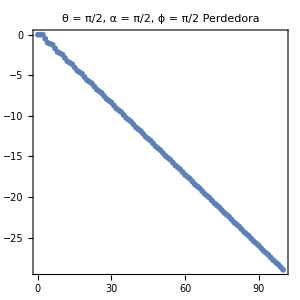

```mathematica
psi0={0.,1.};
θ=π/2;
α=π/2;
ϕ=π/2;
t=100;
probDistTime0=ProbDisTime[psi0,θ,α,ϕ,t];
expval0=ExpecValue[probDistTime0,t];
PlotExpecValue[expval0,θ,α,ϕ,t,
PlotLabel->Column[
{Row[{"θ = ",θ,",  α = ",α,",  ϕ = ",ϕ}],
Row[{ToString[WinningQ[expval0]]}]
},
Alignment->Center
],
ImageSize->300
]
```